## heaterProblemPade (for Problem 2.4)

look at Padé approximation to heater transfer function (expand about s=1)

```mathematica
Clear["Global`*"];
```

```mathematica
G0=Exp[-√s]/(√s); G0mag=Abs[G0/.s->ⅈ ω];
Gp2=PadeApproximant[G0,{s,1,2}]//Simplify;
Gp2mag=Abs[Gp2/.s->ⅈ ω];

Gp3=PadeApproximant[G0,{s,1,3}]//Simplify;
Gp3mag=Abs[Gp3/.s->ⅈ ω];

Gp4=PadeApproximant[G0,{s,1,4}]//Simplify;
Gp4mag=Abs[Gp4/.s->ⅈ ω];
```

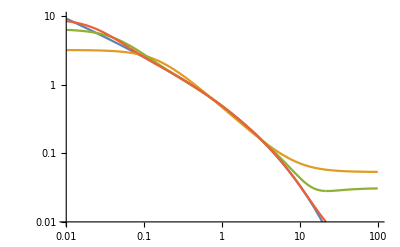

```mathematica
LogLogPlot[{G0mag,Gp2mag,Gp3mag,Gp4mag},{ω,0.01,100},PlotRange->{0.01,10}]
```

```mathematica
Ph0=(Im[G0]/Re[G0])/.s->ⅈ ω; Ph2=(Im[Gp2]/Re[Gp2])/.s->ⅈ ω;
```

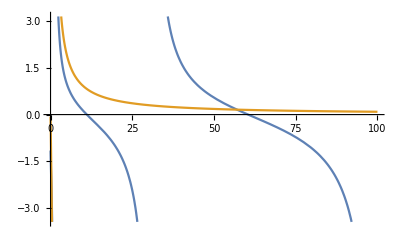

```mathematica
Plot[{Ph0,Ph2},{ω,0.01,100}]
```

```mathematica
{Gp2,Gp3}
```

{(44-76 s+8 s^2)/(5 ⅇ+26 ⅇ s-55 ⅇ s^2),(32701+115029 s-10521 s^2+551 s^3)/(1844 ⅇ+44940 ⅇ s+84468 ⅇ s^2+6508 ⅇ s^3)}

```mathematica
Gp3//TeXForm
```

\frac{551 s^3-10521 s^2+115029 s+32701}{6508 e s^3+84468 e s^2+44940 e s+1844
   e}

```mathematica
Gp1=PadeApproximant[G0,{s,1,1}]//Simplify
```

(9-s)/(ⅇ+7 ⅇ s)

```mathematica
Gp1Taylor = Series[G0,{s,1,4}]//Simplify
```

1/ⅇ-(s-1)/ⅇ+(7 (s-1)^2)/(8 ⅇ)-(37 (s-1)^3)/(48 ⅇ)+(133 (s-1)^4)/(192 ⅇ)+O[s-1]^5

```mathematica
Series[Gp1,{s,1,3}]//Simplify
```

1/ⅇ-(s-1)/ⅇ+(7 (s-1)^2)/(8 ⅇ)-(49 (s-1)^3)/(64 ⅇ)+O[s-1]^4